## Visualization` Documentation

### Preamble

```mathematica
Needs["Visualization`"]
```

The following packages are needed to run some code found in this documentation notebook.

```mathematica
Needs["Tensor`"]
Needs["QuantumSystems`"]
Needs["QSim`"]
```

### Source Code

Open Source Code

## Introduction and Overview

This package provides tools for visualizing and plotting various quantities.

## Matrices

### ComplexMatrixPlot

ComplexMatrixPlot[A] is designed to graphically display complex matrices.The element amplitudes are displayed as heights of a 3D bar graph,with the sign of a height determined by which half of the imaginary plane it lies in,top or bottom.The color of a bar represents the absolute value of its argument;a phase of π/2 and-π/2 will have the same color (but their heights will have opposite signs).

#### Options

The options are simply those of DiscretePlot3D, which is the plotting function used by ComplexMatrixPlot.

Option | Default Value | Description
AlignmentPoint | Center | AlignmentPoint is an option which specifies how objects should by default be aligned when they appear in Inset.
AspectRatio | Automatic | AspectRatio is an option for Graphics and related functions that specifies the ratio of height to width for a plot. 
AutomaticImageSize | False | No description available.
Axes | True | Axes is an option for graphics functions that specifies whether axes should be drawn. 
AxesEdge | Automatic | AxesEdge is an option for three-dimensional graphics functions that specifies on which edges of the bounding box axes should be drawn. 
AxesLabel | None | AxesLabel is an option for graphics functions that specifies labels for axes. 
AxesOrigin | Automatic | AxesOrigin is an option for graphics functions that specifies where any axes drawn should cross. 
AxesStyle | {} | AxesStyle is an option for graphics functions that specifies how axes should be rendered. 
Background | None | Background is an option that specifies what background color to use. 
BaselinePosition | Automatic | BaselinePosition is an option that specifies where the baseline of an object is considered to be for purposes of alignment with surrounding text or other expressions. 
BaseStyle | {} | BaseStyle is an option for formatting and related constructs that specifies the base style to use for them. 
Boxed | True | Boxed is an option for Graphics3D that specifies whether to draw the edges of the bounding box in a three-dimensional picture. 
BoxRatios | {1,1,0.4} | BoxRatios is an option for Graphics3D that gives the ratios of side lengths for the bounding box of the three-dimensional picture. 
BoxStyle | {} | BoxStyle is an option for three-dimensional graphics functions that specifies how the bounding box should be rendered. 
ClipPlanes | None | ClipPlanes is an option to Graphics3D that specifies a list of clipping planes that can cut away portions of a 3D scene from the resulting view.
ClipPlanesStyle | Automatic | ClipPlanesStyle is an option to Graphics3D that specifies how clipping planes defined with the ClipPlanes option should be rendered.
ColorFunction | Automatic | ColorFunction is an option for graphics functions that specifies a function to apply to determine colors of elements. 
ColorFunctionScaling | True | ColorFunctionScaling is an option for graphics functions that specifies whether arguments supplied to a color function should be scaled to lie between 0 and 1. 
ColorOutput | Automatic | ColorOutput is an option for graphics functions that specifies the type of color output to produce. 
ContentSelectable | Automatic | ContentSelectable is an option to constructs such as Inset, Graphics, and GraphicsGroup that specifies whether and how content within them should be selectable. 
ControllerLinking | Automatic | ControllerLinking is an option for Manipulate, Graphics3D, Plot3D, and related functions that specifies whether to allow interactive control by external controllers.
ControllerMethod | Automatic | ControllerMethod is an option for Manipulate, Graphics3D, Plot3D, and related functions that specifies the default way that controls on an external controller device should apply.
ControllerPath | Automatic | ControllerPath is an option that gives a list of external controllers or classes of controllers to try for functions such as ControllerState, Manipulate, and Graphics3D.
CoordinatesToolOptions | Automatic | CoordinatesToolOptions is an option for Graphics that gives values of options associated with the Get Coordinates tool.
DisplayFunction | Identity | DisplayFunction is an option for graphics and sound functions that specifies a function to apply to graphics and sound objects before returning them.
Epilog | {} | Epilog is an option for graphics functions that gives a list of graphics primitives to be rendered after the main part of the graphics is rendered. 
EvaluationMonitor | None | EvaluationMonitor is an option for various numerical computation and plotting functions that gives an expression to evaluate whenever functions derived from the input are evaluated numerically. 
ExtentElementFunction | Automatic | ExtentElementFunction is an option to DiscretePlot and DiscretePlot3D that gives a function to use to generate the primitives for rendering each extent element. 
ExtentMarkers | None | ExtentMarkers is an option to DiscretePlot and DiscretePlot3D that specifies markers to draw at extent boundaries. 
ExtentSize | None | ExtentSize is an option to DiscretePlot and DiscretePlot3D that specifies how far to extend out from each plot point. 
FaceGrids | None | FaceGrids is an option for three-dimensional graphics functions that specifies grid lines to draw on the faces of the bounding box. 
FaceGridsStyle | {} | FaceGridsStyle is an option for 3D graphics functions that specifies how face grids should be rendered.
Filling | Automatic | Filling is an option for ListPlot, Plot, Plot3D, and related functions that specifies what filling to add under points, curves, and surfaces. 
FillingStyle | Automatic | FillingStyle is an option for ListPlot, Plot, Plot3D, and related functions that specifies the default style of filling to be used. 
FormatType | TraditionalForm | FormatType is an option for output streams, graphics, and functions such as Text that specifies the default format type to use when outputting expressions. 
ImageMargins | 0. | ImageMargins is an option that specifies the absolute margins to leave around the image displayed for an object. 
ImagePadding | All | ImagePadding is an option for graphics functions that specifies what absolute extra padding should be left for extended objects such as thick lines and annotations such as tick and axis labels.
ImageSize | Automatic | ImageSize is an option that specifies the overall size of an image to display for an object. 
ImageSizeRaw | Automatic | No description available.
Joined | False | Joined is an option for ListPlot and related functions that specifies whether points in each dataset should be joined into a line, or should be plotted as separate points. 
LabelStyle | {} | LabelStyle is an option for formatting and related constructs that specifies the style to use in displaying their label-like elements. 
Lighting | "Neutral" | Lighting is an option for Graphics3D and related functions that specifies what simulated lighting to use in coloring 3D surfaces. 
Method | Automatic | Method is an option for various algorithm-intensive functions that specifies what internal methods they should use.
PerformanceGoal | "Quality" | PerformanceGoal is an option for plotting and various other algorithmic functions that specifies what aspect of performance to try to optimize with Automatic settings for options.
PlotLabel | None | PlotLabel is an option for graphics functions that specifies an overall label for a plot. 
PlotLegends | None | PlotLegends is an option for plot functions that specifies what legends to use. 
PlotMarkers | None | PlotMarkers is an option for graphics functions like ListPlot and ListLinePlot that specifies what markers to draw at the points plotted. 
PlotRange | {Full,Full,Automatic} | PlotRange is an option for graphics functions that specifies what range of coordinates to include in a plot. 
PlotRangePadding | Automatic | PlotRangePadding is an option for graphics functions that specifies how much further axes etc. should extend beyond the range of coordinates specified by PlotRange. 
PlotRegion | Automatic | PlotRegion is an option for graphics functions that specifies what region of the final display area a plot should fill. 
PlotStyle | Automatic | PlotStyle is an option for plotting and related functions that specifies styles in which objects are to be drawn. 
PlotTheme | Automatic | PlotTheme is an option for plotting and related functions that specifies an overall theme for visualization elements and styles. 
PreserveImageOptions | Automatic | PreserveImageOptions is an option to graphics and related functions that specifies whether image size and certain other options should be preserved from the previous version of a graphic if the graphic is replaced by a new one in output.
Prolog | {} | Prolog is an option for graphics functions which gives a list of graphics primitives to be rendered before the main part of the graphics is rendered. 
RegionFunction | True& | RegionFunction is an option for plotting functions that specifies the region to include in the plot drawn. 
RotationAction | "Fit" | RotationAction is an option for three-dimensional graphics functions that specifies how to render 3D objects when they are interactively rotated.
SphericalRegion | False | SphericalRegion is an option for three-dimensional graphics functions that specifies whether the final image should be scaled so that a sphere drawn around the three-dimensional bounding box would fit in the display area specified. 
Ticks | Automatic | Ticks is an option for graphics functions that specifies tick marks for axes. 
TicksStyle | {} | TicksStyle is an option for graphics functions which specifies how ticks should be rendered.
TouchscreenAutoZoom | False | TouchscreenAutoZoom is an option for Manipulate and Graphics3D that determines whether the interface zooms to full-screen when it is activated by touching it on supported touch screen platforms.
ViewAngle | Automatic | ViewAngle is an option for Graphics3D and related functions that gives the opening angle for a simulated camera used to view the three-dimensional scene. 
ViewCenter | Automatic | ViewCenter is an option for Graphics3D and related functions which gives the scaled coordinates of the point which should appear at the center of the final image. 
ViewMatrix | Automatic | ViewMatrix is an option for Graphics3D and related functions that can be used to specify a pair of explicit homogeneous transformation and projection matrices for 3D coordinates.
ViewPoint | {1.3,-2.4,2.} | ViewPoint is an option for Graphics3D and related functions which gives the point in space from which three-dimensional objects are to be viewed. 
ViewRange | All | ViewRange is an option for Graphics3D and related functions which specifies the range of distances from the view point to be included in displaying a three-dimensional scene. 
ViewVector | Automatic | ViewVector is an option for Graphics3D and related functions which specifies the position and direction of a simulated camera used to view three-dimensional objects. 
ViewVertical | {0,0,1} | ViewVertical is an option for Graphics3D and related functions which specifies what direction in scaled coordinates should be vertical in the final image. 
WorkingPrecision | MachinePrecision | WorkingPrecision is an option for various numerical operations that specifies how many digits of precision should be maintained in internal computations.

#### Example 1

Positive and negative numbers can be seen as the phases 0 and π.

```mathematica
RandomReal[{-1,1},{5,5}]//ComplexMatrixPlot
```

-Graphics3D-

#### Example 2

Conjugate symmetry can be spotted with color symmetry across the diagonal.

```mathematica
With[{A=RandomReal[{-1,1},{3,3}]+I RandomReal[{-1,1},{3,3}]},A+A†]//ComplexMatrixPlot
```

-Graphics3D-

### BlockForm

BlockForm[A,n] is similar to MatrixForm, but prints the matrix A in block form with dividers every n columns and rows. If the argument n is omitted, Length[A]/p is assumed,where p is the smallest prime factor of Length[A].

#### Example

```mathematica
RandomReal[{-1,1},{6,6}]//BlockForm
```

(-0.234957 | -0.42005 | 0.832704 | 0.396351 | 0.83863 | -0.34012
0.60201 | 0.945962 | 0.159497 | -0.458117 | -0.860078 | -0.357849
0.0308752 | 0.0555474 | 0.949346 | 0.604616 | -0.90881 | -0.174735
0.622201 | 0.596818 | 0.92215 | -0.598748 | -0.861557 | -0.291257
-0.301819 | -0.58871 | 0.557752 | 0.745451 | -0.11071 | -0.267965
-0.0280371 | 0.551633 | 0.204659 | -0.442758 | 0.743721 | 0.308073)

```mathematica
BlockForm[RandomReal[{-1,1},{6,6}],2]
```

(-0.947833 | 0.293469 | -0.553499 | 0.173947 | 0.644774 | 0.895452
-0.681973 | -0.110814 | -0.78522 | -0.448715 | 0.751269 | 0.514533
-0.855871 | -0.933086 | 0.108773 | -0.529716 | 0.464754 | 0.900501
0.715862 | -0.979174 | -0.790914 | -0.163293 | 0.217857 | -0.898311
-0.758427 | -0.215302 | -0.270154 | -0.615916 | 0.446297 | 0.657159
0.03508 | 0.918425 | 0.69997 | -0.0868351 | -0.129963 | -0.161875)

### MatrixListForm

MatrixListForm[{A1,A2,...}] inteprets a 3D tensor as a list of matrices and displays it as such; a generalization of MatrixForm.

#### Example

```mathematica
{TP[XX],TP[YY],TP[ZZ]}//MatrixListForm
```

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)

## Bloch Plots

### BlochPlot

BlochPlot[state] plots state on a 3D Bloch sphere,where the state can be a qubit pure state or a density matrix.
BlochPlot[{state1,state2,...}] plots the given qubit states on a 3D Bloch sphere, where the all of the states are pure or a density matrices.
BlochPlot[{{state11,state12,...},{state21,state22,...},...}] plots the given qubit states on a 3D Bloch sphere, where the all of the states are pure or a density matrices. The collections {statej1,statej2,...} are treated as separate trajectories, and each with their own color scheme.

Options
• All options from Graphics3D, ParametricPlot3D, and Interpolation are valid and are passed to their respective functions.
• Additionally:
 | ◻ BlochPlotColors determines the color scheme of each trajectory or set of states. It can be a list of colors,in which case Blend will be taken of each color and Lighter of that color. It can also be a list of pairs of colors,where a Blend is taken of each pair.or not 
 | ◻ BlochPlotJoined specifies whether or not each trajectory should be interpolated. In each case a different plotting method is used.
 | ◻ BlochPlotEndPoints specifies whether or not the end points of a trajectory should be differentiated from intermediate points of the trajectory,True or False.  
 | ◻ BlochPlotLabels can be Off or a list of labels to use in a legend.

Notes
• You cannot mix and match pure states and density matrices.
• Trajectories with only one state get a line to the origin drawn.

Tip
• Setting ViewAngle (usually to around 0.3) can reduce whitespace, but may also clip some labels.

#### Options

BlochPlotColors is an option for BlochPlot and BlochPlot2D. It specifies the color scheme of each list of density matrices entered.

BlochPlotEndPoints is an option for BlochPlot which specifies whether or not end points of a trajectory should be differentiated from intermediate points.

BlochPlotJoined is an option for BlochPlot and BlochPlot2D which specifies whether trajectories should be interpolated or not. This forks the code into the use of ParametricPlot(3D) or a list of Points in Graphics(3D).

BlochPlotLabels is an option for BlochPlot and BlochPlot2D which specifies a list of labels to use in the legend.

Option | Default Value | Description
ViewAngle | 0.34 | ViewAngle is an option for Graphics3D and related functions that gives the opening angle for a simulated camera used to view the three-dimensional scene. 
BlochPlotLabels | Off | BlochPlotLabels is an option for BlochPlot and BlochPlot2D which specifies a list of labels to use in the legend.
BlochPlotJoined | False | BlochPlotJoined is an option for BlochPlot and BlochPlot2D which specifies whether trajectories should be interpolated or not. This forks the code into the use of ParametricPlot(3D) or a list of Points in Graphics(3D).
BlochPlotColors | Automatic | BlochPlotColors is an option for BlochPlot and BlochPlot2D. It specifies the color scheme of each list of density matrices entered.
BlochPlotEndPoints | True | BlochPlotEndPoints is an option for BlochPlot which specifies whether or not end points of a trajectory should be differentiated from intermediate points.
AlignmentPoint | Center | AlignmentPoint is an option which specifies how objects should by default be aligned when they appear in Inset.
AspectRatio | Automatic | AspectRatio is an option for Graphics and related functions that specifies the ratio of height to width for a plot. 
AutomaticImageSize | False | No description available.
Axes | False | Axes is an option for graphics functions that specifies whether axes should be drawn. 
AxesEdge | Automatic | AxesEdge is an option for three-dimensional graphics functions that specifies on which edges of the bounding box axes should be drawn. 
AxesLabel | None | AxesLabel is an option for graphics functions that specifies labels for axes. 
AxesOrigin | Automatic | AxesOrigin is an option for graphics functions that specifies where any axes drawn should cross. 
AxesStyle | {} | AxesStyle is an option for graphics functions that specifies how axes should be rendered. 
Background | None | Background is an option that specifies what background color to use. 
BaselinePosition | Automatic | BaselinePosition is an option that specifies where the baseline of an object is considered to be for purposes of alignment with surrounding text or other expressions. 
BaseStyle | {} | BaseStyle is an option for formatting and related constructs that specifies the base style to use for them. 
Boxed | True | Boxed is an option for Graphics3D that specifies whether to draw the edges of the bounding box in a three-dimensional picture. 
BoxRatios | Automatic | BoxRatios is an option for Graphics3D that gives the ratios of side lengths for the bounding box of the three-dimensional picture. 
BoxStyle | {} | BoxStyle is an option for three-dimensional graphics functions that specifies how the bounding box should be rendered. 
ClipPlanes | None | ClipPlanes is an option to Graphics3D that specifies a list of clipping planes that can cut away portions of a 3D scene from the resulting view.
ClipPlanesStyle | Automatic | ClipPlanesStyle is an option to Graphics3D that specifies how clipping planes defined with the ClipPlanes option should be rendered.
ColorOutput | Automatic | ColorOutput is an option for graphics functions that specifies the type of color output to produce. 
ContentSelectable | Automatic | ContentSelectable is an option to constructs such as Inset, Graphics, and GraphicsGroup that specifies whether and how content within them should be selectable. 
ControllerLinking | Automatic | ControllerLinking is an option for Manipulate, Graphics3D, Plot3D, and related functions that specifies whether to allow interactive control by external controllers.
ControllerMethod | Automatic | ControllerMethod is an option for Manipulate, Graphics3D, Plot3D, and related functions that specifies the default way that controls on an external controller device should apply.
ControllerPath | Automatic | ControllerPath is an option that gives a list of external controllers or classes of controllers to try for functions such as ControllerState, Manipulate, and Graphics3D.
CoordinatesToolOptions | Automatic | CoordinatesToolOptions is an option for Graphics that gives values of options associated with the Get Coordinates tool.
DisplayFunction | Identity | DisplayFunction is an option for graphics and sound functions that specifies a function to apply to graphics and sound objects before returning them.
Epilog | {} | Epilog is an option for graphics functions that gives a list of graphics primitives to be rendered after the main part of the graphics is rendered. 
FaceGrids | None | FaceGrids is an option for three-dimensional graphics functions that specifies grid lines to draw on the faces of the bounding box. 
FaceGridsStyle | {} | FaceGridsStyle is an option for 3D graphics functions that specifies how face grids should be rendered.
FormatType | TraditionalForm | FormatType is an option for output streams, graphics, and functions such as Text that specifies the default format type to use when outputting expressions. 
ImageMargins | 0. | ImageMargins is an option that specifies the absolute margins to leave around the image displayed for an object. 
ImagePadding | All | ImagePadding is an option for graphics functions that specifies what absolute extra padding should be left for extended objects such as thick lines and annotations such as tick and axis labels.
ImageSize | Automatic | ImageSize is an option that specifies the overall size of an image to display for an object. 
ImageSizeRaw | Automatic | No description available.
LabelStyle | {} | LabelStyle is an option for formatting and related constructs that specifies the style to use in displaying their label-like elements. 
Lighting | Automatic | Lighting is an option for Graphics3D and related functions that specifies what simulated lighting to use in coloring 3D surfaces. 
Method | Automatic | Method is an option for various algorithm-intensive functions that specifies what internal methods they should use.
PlotLabel | None | PlotLabel is an option for graphics functions that specifies an overall label for a plot. 
PlotRange | All | PlotRange is an option for graphics functions that specifies what range of coordinates to include in a plot. 
PlotRangePadding | Automatic | PlotRangePadding is an option for graphics functions that specifies how much further axes etc. should extend beyond the range of coordinates specified by PlotRange. 
PlotRegion | Automatic | PlotRegion is an option for graphics functions that specifies what region of the final display area a plot should fill. 
PreserveImageOptions | Automatic | PreserveImageOptions is an option to graphics and related functions that specifies whether image size and certain other options should be preserved from the previous version of a graphic if the graphic is replaced by a new one in output.
Prolog | {} | Prolog is an option for graphics functions which gives a list of graphics primitives to be rendered before the main part of the graphics is rendered. 
RotationAction | "Fit" | RotationAction is an option for three-dimensional graphics functions that specifies how to render 3D objects when they are interactively rotated.
SphericalRegion | False | SphericalRegion is an option for three-dimensional graphics functions that specifies whether the final image should be scaled so that a sphere drawn around the three-dimensional bounding box would fit in the display area specified. 
Ticks | Automatic | Ticks is an option for graphics functions that specifies tick marks for axes. 
TicksStyle | {} | TicksStyle is an option for graphics functions which specifies how ticks should be rendered.
TouchscreenAutoZoom | False | TouchscreenAutoZoom is an option for Manipulate and Graphics3D that determines whether the interface zooms to full-screen when it is activated by touching it on supported touch screen platforms.
ViewCenter | Automatic | ViewCenter is an option for Graphics3D and related functions which gives the scaled coordinates of the point which should appear at the center of the final image. 
ViewMatrix | Automatic | ViewMatrix is an option for Graphics3D and related functions that can be used to specify a pair of explicit homogeneous transformation and projection matrices for 3D coordinates.
ViewPoint | {1.3,-2.4,2.} | ViewPoint is an option for Graphics3D and related functions which gives the point in space from which three-dimensional objects are to be viewed. 
ViewRange | All | ViewRange is an option for Graphics3D and related functions which specifies the range of distances from the view point to be included in displaying a three-dimensional scene. 
ViewVector | Automatic | ViewVector is an option for Graphics3D and related functions which specifies the position and direction of a simulated camera used to view three-dimensional objects. 
ViewVertical | {0,0,1} | ViewVertical is an option for Graphics3D and related functions which specifies what direction in scaled coordinates should be vertical in the final image. 
BoundaryStyle | None | BoundaryStyle is an option for plotting functions that specifies the style in which boundaries of regions should be drawn. 
ColorFunction | Automatic | ColorFunction is an option for graphics functions that specifies a function to apply to determine colors of elements. 
ColorFunctionScaling | True | ColorFunctionScaling is an option for graphics functions that specifies whether arguments supplied to a color function should be scaled to lie between 0 and 1. 
Evaluated | Automatic | No description available.
EvaluationMonitor | None | EvaluationMonitor is an option for various numerical computation and plotting functions that gives an expression to evaluate whenever functions derived from the input are evaluated numerically. 
Exclusions | Automatic | Exclusions is an option that specifies where to exclude in regions used by functions like Plot, Plot3D, and NIntegrate.
ExclusionsStyle | None | ExclusionsStyle is an option to plotting functions that specifies how to render subregions excluded according to Exclusions. 
MaxRecursion | Automatic | MaxRecursion is an option for functions like NIntegrate and Plot that specifies how many recursive subdivisions can be made. 
Mesh | Automatic | Mesh is an option for Plot3D, DensityPlot, and other plotting functions that specifies what mesh should be drawn. 
MeshFunctions | Automatic | MeshFunctions is an option for plotting functions that specifies functions to use to determine the placement of mesh divisions. 
MeshShading | None | MeshShading is an option for plotting functions that gives lists of colors to use for regions between mesh divisions. 
MeshStyle | Automatic | MeshStyle is an option for Plot3D, DensityPlot, and other plotting functions that specifies the style in which to draw a mesh. 
NormalsFunction | Automatic | NormalsFunction is an option for Plot3D and related functions that specifies a function to apply to determine the effective surface normals at every point.
PerformanceGoal | "Quality" | PerformanceGoal is an option for plotting and various other algorithmic functions that specifies what aspect of performance to try to optimize with Automatic settings for options.
PlotLegends | None | PlotLegends is an option for plot functions that specifies what legends to use. 
PlotPoints | Automatic | PlotPoints is an option for plotting functions that specifies how many initial sample points to use. 
PlotStyle | Automatic | PlotStyle is an option for plotting and related functions that specifies styles in which objects are to be drawn. 
PlotTheme | Automatic | PlotTheme is an option for plotting and related functions that specifies an overall theme for visualization elements and styles. 
RegionFunction | True& | RegionFunction is an option for plotting functions that specifies the region to include in the plot drawn. 
TargetUnits | Automatic | TargetUnits is an option used to specify the desired output units for visualization functions operating on Quantity expressions.
TextureCoordinateFunction | Automatic | TextureCoordinateFunction is an option to Plot3D and similar functions that specifies a function that computes texture coordinates.
TextureCoordinateScaling | Automatic | TextureCoordinateScaling is an option to Plot3D and similar functions that specifies whether arguments supplied to a texture coordinate function should be scaled to lie between 0 and 1.
WorkingPrecision | MachinePrecision | WorkingPrecision is an option for various numerical operations that specifies how many digits of precision should be maintained in internal computations. 
InterpolationOrder | 3 | InterpolationOrder is an option for Interpolation, as well as ListLinePlot, ListPlot3D, ListContourPlot, and related functions, that specifies what order of interpolation to use.
PeriodicInterpolation | False | No description available.

#### Example 1

Plot a single pure state on the Bloch sphere. Trajectories with only one state get a line to the origin.

```mathematica
BlochPlot[{Sqrt[I 2/3],Sqrt[1/3]}]
```

-Graphics3D-

A list of states is interpretted as a trajectory and gets the same color scheme.

```mathematica
BlochPlot[{{Sqrt[I 2/3],Sqrt[1/3]},{1,0},{0,1}},BlochPlotLabels->{1,2,3}]
```

-Graphics3D-

However, adding an extra layer of lists, each list of states is interpretted as a separate trajectory.

```mathematica
BlochPlot[{{{Sqrt[I 2/3],Sqrt[1/3]}},{{1,0},{Sqrt[0.99],Sqrt[1-0.99]}},{{0,1}}},BlochPlotLabels->{1,2,3}]
```

-Graphics3D-

#### Example 2

```mathematica
BlochPlot[Table[RandomDensity[2],{n,50}],BlochPlotEndPoints->#,ImageSize->350,PlotLegends->On]&/@{True,False}//Row
```

-Graphics3D--Graphics3D-

#### Example 3

Use EvalPulse to generate two lists of states.

```mathematica
states1=States@EvalPulse[Sin[10 #] TP[X]+4TP[Z]&,π,PollingInterval->0.05,InitialState->TP[U]];
states2=States@EvalPulse[TP[X],π/2,PollingInterval->0.1,InitialState->TP[U]];
```

Demonstrate the difference between interpolated and uninterpolated:

```mathematica
BlochPlot[{states1,states2},
BlochPlotJoined->#,
ImageSize->350,
BlochPlotLabels->{"First","Second"}
]&/@{False,True}//Row
```

-Graphics3D--Graphics3D-

Use a custom color scheme.

```mathematica
BlochPlot[{states1,states2},
BlochPlotJoined->#,
ImageSize->350,
BlochPlotLabels->{"First","Second"},
BlochPlotColors->{{Red,Yellow},{Magenta,Cyan}}
]&/@{False,True}//Row
```

-Graphics3D--Graphics3D-

#### Example 4

Various orders of Interpolation for 4 pure states in a single trajectory.

```mathematica
BlochPlot[{{1,0},{0,1},{1,1}/Sqrt[2],{I,1}/Sqrt[2]},
BlochPlotJoined->True,
InterpolationOrder->#,
ImageSize->200
]&/@Range[3]//Row
```

-Graphics3D--Graphics3D--Graphics3D-

#### Example 5

Note: to use this example, you need to run the Preamble at the top, and then run the cell below.

Set the ViewPoint to a dynamic variable to sync the rotation of multiple Bloch spheres.

```mathematica
states1=States@EvalPulse[Sin[10 #] TP[X]+4TP[Z]&,π,PollingInterval->0.05,InitialState->TP[U]];
states2=States@EvalPulse[TP[X],π/2,PollingInterval->0.1,InitialState->TP[U]];

vp=Options[Graphics3D,ViewPoint][[1,2]];

BlochPlot[{states1,states2},
BlochPlotJoined->#,
ImageSize->350,
BlochPlotLabels->{"First","Second"},
ViewPoint->Dynamic[vp]
]&/@{False,True}//Row
```

-Graphics3D--Graphics3D-

### BlochPlot2D

BlochPlot2D[state] plots state onto XZ, YZ, and XY  2D projections,where the state can be a pure state or a density matrix.

#### Example

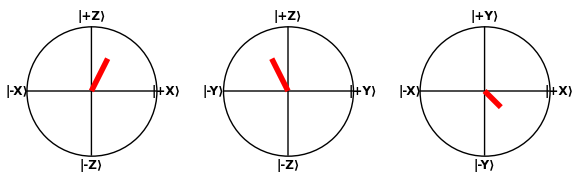

```mathematica
BlochPlot2D[0.5*{{1,0},{0,0}}+0.25*{{1,1},{1,1}}/2+0.25*{{1,I},{-I,1}}/2]
```

### ListBlochPlot2D

ListBlochPlot2D[states] plots a list of states onto XZ, YZ, and XY 2D projections, where the states can be a list of pure state vectors or a list of density matrix.

#### Example

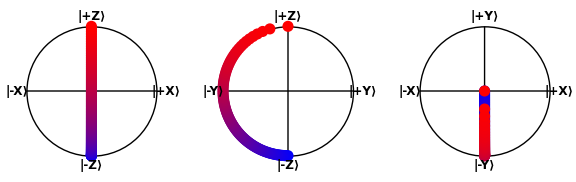

```mathematica
ListBlochPlot2D[Map[{#,-I √(1-#^2)}&,Range[0,1,0.01]]]
```

## Eigensystems

### EigensystemForm

EigensystemForm[sys] takes an eigensystem sys in the form as outputted by Eigensystem and prints it in a readable way.

#### Example

```mathematica
Eigensystem[TP[XX]]//EigensystemForm
```

-1 | -1 | 1 | 1
↓ | ↓ | ↓ | ↓
(-1
0
0
1) | (0
-1
1
0) | (1
0
0
1) | (0
1
1
0)

## Special Plotting Functions

### FourierListPlot

FourierListPlot[data,{mint,maxt},function] is very similar to ListPlot[data],except that the (single sided spectrum) discrete Fourier transform of data (or each sublist thereof) is plotted. mint and maxt are the minimum and maximum time domain points,with an assumed linear spacing on the data.function is a function or list of functions you want to plot,eg. Abs,or {Re,Im}. All options available to ListPlot may be added,e.g. Joined→True.Of special note is DataRange, which must either be Automatic or {minf,maxf} which are in units of frequency.

#### Options

We have all the options from ListPlot.

Option | Default Value | Description
AlignmentPoint | Center | AlignmentPoint is an option which specifies how objects should by default be aligned when they appear in Inset.
AspectRatio | 1/GoldenRatio | AspectRatio is an option for Graphics and related functions that specifies the ratio of height to width for a plot. 
Axes | True | Axes is an option for graphics functions that specifies whether axes should be drawn. 
AxesLabel | None | AxesLabel is an option for graphics functions that specifies labels for axes. 
AxesOrigin | Automatic | AxesOrigin is an option for graphics functions that specifies where any axes drawn should cross. 
AxesStyle | {} | AxesStyle is an option for graphics functions that specifies how axes should be rendered. 
Background | None | Background is an option that specifies what background color to use. 
BaselinePosition | Automatic | BaselinePosition is an option that specifies where the baseline of an object is considered to be for purposes of alignment with surrounding text or other expressions. 
BaseStyle | {} | BaseStyle is an option for formatting and related constructs that specifies the base style to use for them. 
ClippingStyle | None | ClippingStyle is an option for plotting functions that specifies the style of what should be drawn when curves or surfaces would extend beyond the plot range. 
ColorFunction | Automatic | ColorFunction is an option for graphics functions that specifies a function to apply to determine colors of elements. 
ColorFunctionScaling | True | ColorFunctionScaling is an option for graphics functions that specifies whether arguments supplied to a color function should be scaled to lie between 0 and 1. 
ColorOutput | Automatic | ColorOutput is an option for graphics functions that specifies the type of color output to produce. 
ContentSelectable | Automatic | ContentSelectable is an option to constructs such as Inset, Graphics, and GraphicsGroup that specifies whether and how content within them should be selectable. 
CoordinatesToolOptions | Automatic | CoordinatesToolOptions is an option for Graphics that gives values of options associated with the Get Coordinates tool.
DataRange | Automatic | DataRange is an option for functions such as ListPlot and ListDensityPlot that specifies what range of actual coordinates the data should be assumed to occupy. 
DisplayFunction | Identity | DisplayFunction is an option for graphics and sound functions that specifies a function to apply to graphics and sound objects before returning them.
Epilog | {} | Epilog is an option for graphics functions that gives a list of graphics primitives to be rendered after the main part of the graphics is rendered. 
Filling | None | Filling is an option for ListPlot, Plot, Plot3D, and related functions that specifies what filling to add under points, curves, and surfaces. 
FillingStyle | Automatic | FillingStyle is an option for ListPlot, Plot, Plot3D, and related functions that specifies the default style of filling to be used. 
FormatType | TraditionalForm | FormatType is an option for output streams, graphics, and functions such as Text that specifies the default format type to use when outputting expressions. 
Frame | False | Frame is an option for Graphics, Grid, and other constructs that specifies whether to include a frame. 
FrameLabel | None | FrameLabel is an option for Graphics, Manipulate, and related functions that specifies labels to be placed on the edges of a frame. 
FrameStyle | {} | FrameStyle is an option for Graphics, Grid, and other constructs that specifies the style in which to draw frames.
FrameTicks | Automatic | FrameTicks is an option for 2D graphics functions that specifies tick marks for the edges of a frame. 
FrameTicksStyle | {} | FrameTicksStyle is an option for 2D graphics functions that specifies how frame ticks should be rendered.
GridLines | None | GridLines is an option for two-dimensional graphics functions that specifies grid lines. 
GridLinesStyle | {} | GridLinesStyle is an option for 2D graphics functions that specifies how grid lines should be rendered.
ImageMargins | 0. | ImageMargins is an option that specifies the absolute margins to leave around the image displayed for an object. 
ImagePadding | All | ImagePadding is an option for graphics functions that specifies what absolute extra padding should be left for extended objects such as thick lines and annotations such as tick and axis labels.
ImageSize | Automatic | ImageSize is an option that specifies the overall size of an image to display for an object. 
ImageSizeRaw | Automatic | No description available.
InterpolationOrder | None | InterpolationOrder is an option for Interpolation, as well as ListLinePlot, ListPlot3D, ListContourPlot, and related functions, that specifies what order of interpolation to use.
Joined | False | Joined is an option for ListPlot and related functions that specifies whether points in each dataset should be joined into a line, or should be plotted as separate points. 
LabelStyle | {} | LabelStyle is an option for formatting and related constructs that specifies the style to use in displaying their label-like elements. 
MaxPlotPoints | ∞ | MaxPlotPoints is an option for plotting functions like ArrayPlot and ListPlot3D that specifies the maximum number of points that will explicitly be included in the output. 
Mesh | None | Mesh is an option for Plot3D, DensityPlot, and other plotting functions that specifies what mesh should be drawn. 
MeshFunctions | {#1&} | MeshFunctions is an option for plotting functions that specifies functions to use to determine the placement of mesh divisions. 
MeshShading | None | MeshShading is an option for plotting functions that gives lists of colors to use for regions between mesh divisions. 
MeshStyle | Automatic | MeshStyle is an option for Plot3D, DensityPlot, and other plotting functions that specifies the style in which to draw a mesh. 
Method | Automatic | Method is an option for various algorithm-intensive functions that specifies what internal methods they should use.
PerformanceGoal | "Quality" | PerformanceGoal is an option for plotting and various other algorithmic functions that specifies what aspect of performance to try to optimize with Automatic settings for options.
PlotLabel | None | PlotLabel is an option for graphics functions that specifies an overall label for a plot. 
PlotLegends | None | PlotLegends is an option for plot functions that specifies what legends to use. 
PlotMarkers | None | PlotMarkers is an option for graphics functions like ListPlot and ListLinePlot that specifies what markers to draw at the points plotted. 
PlotRange | Automatic | PlotRange is an option for graphics functions that specifies what range of coordinates to include in a plot. 
PlotRangeClipping | True | PlotRangeClipping is an option for graphics functions that specifies whether graphics objects should be clipped at the edge of the region defined by PlotRange, or should be allowed to extend to the actual edge of the image. 
PlotRangePadding | Automatic | PlotRangePadding is an option for graphics functions that specifies how much further axes etc. should extend beyond the range of coordinates specified by PlotRange. 
PlotRegion | Automatic | PlotRegion is an option for graphics functions that specifies what region of the final display area a plot should fill. 
PlotStyle | Automatic | PlotStyle is an option for plotting and related functions that specifies styles in which objects are to be drawn. 
PlotTheme | Automatic | PlotTheme is an option for plotting and related functions that specifies an overall theme for visualization elements and styles. 
PreserveImageOptions | Automatic | PreserveImageOptions is an option to graphics and related functions that specifies whether image size and certain other options should be preserved from the previous version of a graphic if the graphic is replaced by a new one in output.
Prolog | {} | Prolog is an option for graphics functions which gives a list of graphics primitives to be rendered before the main part of the graphics is rendered. 
RotateLabel | True | RotateLabel is an option for graphics and related functions that specifies whether labels on vertical frame axes should be rotated to be vertical. 
TargetUnits | Automatic | TargetUnits is an option used to specify the desired output units for visualization functions operating on Quantity expressions.
Ticks | Automatic | Ticks is an option for graphics functions that specifies tick marks for axes. 
TicksStyle | {} | TicksStyle is an option for graphics functions which specifies how ticks should be rendered.

#### Simple Example

Put additive noise on two superimposed frequencies. The time domain runs from 0 to 2.

```mathematica
data=Table[RandomReal[{-.1,.1}]+Exp[-t/0.5](Sin[2π 5 t]+Cos[2π 8 t]),{t,0,2,0.01}];
```

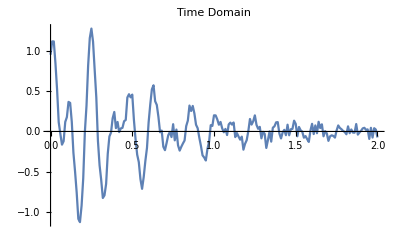

```mathematica
ListPlot[{Range[0,2,0.01],data}ᵀ,PlotRange->All,Joined->True,PlotLabel->"Time Domain"]
```

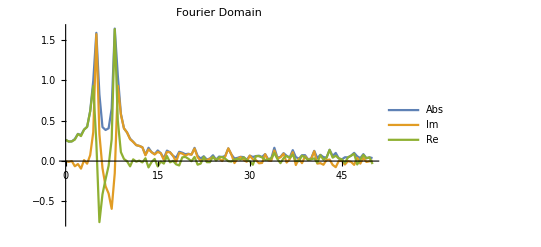

```mathematica
FourierListPlot[data,{0,2},{Abs,Im,Re},PlotRange->All,Joined->True,PlotLegends->{Abs,Im,Re},PlotLabel->"Fourier Domain"]
```

#### Multiple Datasets

Multiple data sets can be entered at the same time.

```mathematica
data1=Table[RandomReal[{-.1,.1}]+Exp[-t/0.5](Cos[2π 10 t]),{t,0,2,0.01}];
data2=Table[RandomReal[{-.1,.1}]+Exp[-t/0.5](Cos[2π 20 t]),{t,0,2,0.01}];
```

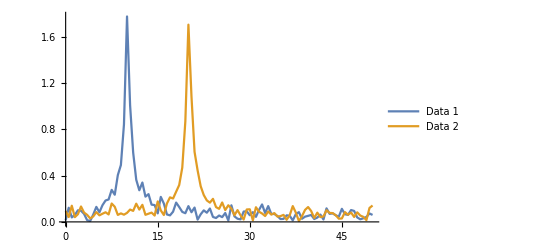

```mathematica
FourierListPlot[{data1,data2},{0,2},Abs,PlotRange->All,Joined->True,PlotLegends->{"Data 1", "Data 2"}]
```

#### Spectrum PlotRange

We can use PlotRange to zoom in on a portion of the spectrum.

```mathematica
data=Table[RandomReal[{-.1,.1}]+Exp[-t/0.5](Sin[2π 5 t]+Cos[2π 8 t]),{t,0,2,0.01}];
```

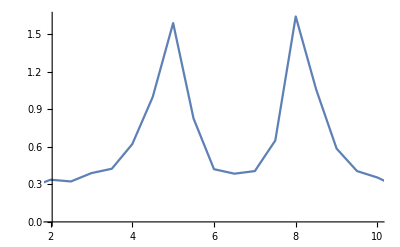

```mathematica
FourierListPlot[data,{0,2},Abs,PlotRange->{{2,10},All},Joined->True]
```